# Versuch 31

```mathematica
ClearAll["Global`*"]
```

## Plot Settings

```mathematica
pltsettings={Frame->True,Axes->False,FrameStyle->Directive[Black,Thickness[0.003]],ImageSize->700,FrameTicksStyle->Directive[Black,15],GridLines->Automatic,GridLinesStyle->Directive[Gray,Thickness[0.002],Opacity[0.8]]};
```

```mathematica
ungewichteterReg[xdata_,ydata_]:=Module[{sx2=Total[xdata^2],sy=Total[ydata],sx=Total[xdata],sxy=Sum[xdata[[i]]ydata[[i]],{i,1,Length[xdata]}], n=Length[xdata],Δ,a,b,σ},Δ=(n sx2-sx^2);a=1/Δ(sx2 sy-sx sxy); b=1/Δ(n sxy-sx sy);σ=Sqrt[1/(n-2) Sum[(ydata[[i]]-a - b xdata[[i]])^2,{i,1,n}]];{a,b,σ Sqrt[sx2/Δ], σ Sqrt[n/Δ]}]
```

## Import Data

```mathematica
rawData=Import[NotebookDirectory[]<>"Irreversibilität der Hysteresekurve.txt"];
```

```mathematica
data=Map[StringReplace["E"->"*10^"],Map[StringReplace[","->"."],StringSplit[StringSplit[rawData,"\n"],"	"]]][[2;;]];
```

```mathematica
data=Map[ToExpression,data,{2}];
```

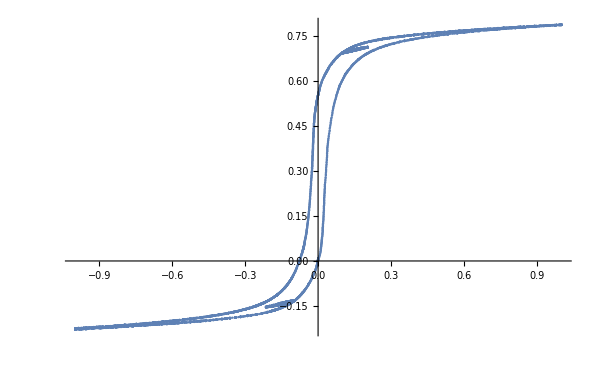

```mathematica
ListPlot[data[[All,{2,3}]]]
```

## Parameters

```mathematica
da=260*10^(-3);
di=220*10^(-3);
h=30*10^(-3);
```

```mathematica
N1=1010;
d=(da+di)/2;
R=0.2;
```

```mathematica
N2=53;
A=h (da-di)/2;
messbereich=100;
fullfaktor=1;
```

```mathematica
dataProcessed={N1 #[[1]]/(π d R),(messbereich/1000)((#1⟦2⟧)/(N2 fullfaktor A))}&/@data[[All,{2,3}]];
```

```mathematica
xpos = (Max[dataProcessed[[All,1]]]+Min[dataProcessed[[All,1]]])/2
ypos = (Max[dataProcessed[[All,2]]]+Min[dataProcessed[[All,2]]])/2
```

6.69777

0.878931

```mathematica
dataShifted={#[[1]]-xpos,#[[2]]-ypos}&/@dataProcessed;
```

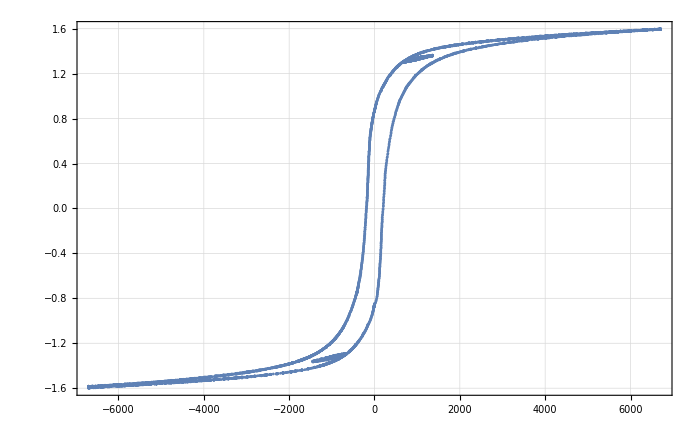

```mathematica
ListPlot[dataShifted,pltsettings]
```

## Export

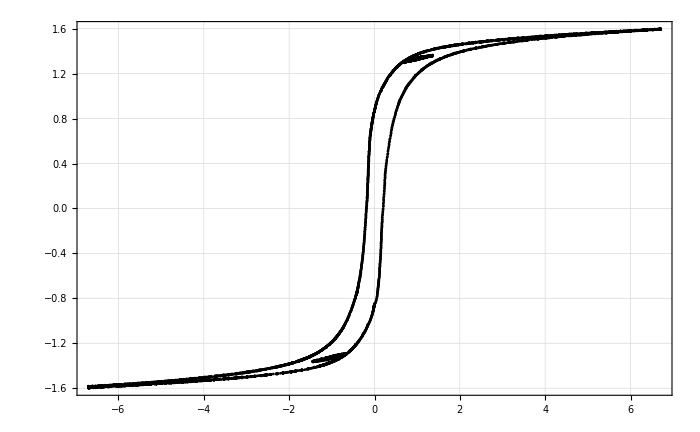

```mathematica
ListPlot[{#[[1]]/1000,#[[2]]}&/@dataShifted,pltsettings,PlotStyle->Black]
```

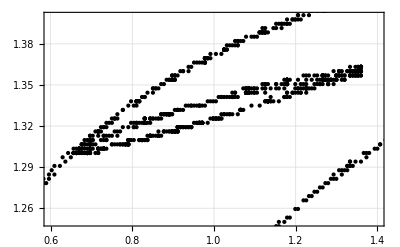

```mathematica
ListPlot[{#[[1]]/1000,#[[2]]}&/@dataShifted,PlotStyle->Directive[Black,PointSize[0.0075]],PlotRange->{{0.6,1.4},{1.25,1.4}},Frame->True,Axes->False,FrameStyle->Directive[Black,Thickness[0.003]],ImageSize->400,FrameTicksStyle->Directive[Black,10],GridLines->Automatic,GridLinesStyle->Directive[Gray,Thickness[0.002],Opacity[0.8]]]
```

```mathematica
Export[NotebookDirectory[]<>"abbildungen/irreversibilitat raw.pdf",ListPlot[{#[[1]]/1000,#[[2]]}&/@dataShifted,pltsettings,PlotStyle->Black],Background->None];
Export[NotebookDirectory[]<>"abbildungen/irreversibilitat subplot raw.pdf",ListPlot[{#[[1]]/1000,#[[2]]}&/@dataShifted,PlotStyle->Directive[Black,PointSize[0.0075]],PlotRange->{{0.6,1.4},{1.25,1.4}},Frame->True,Axes->False,FrameStyle->Directive[Black,Thickness[0.003]],ImageSize->400,FrameTicksStyle->Directive[Black,10],GridLines->Automatic,GridLinesStyle->Directive[Gray,Thickness[0.002],Opacity[0.8]]],Background->None];
```